```mathematica
EchoTemporary=(PrintTemporary[#]; #)&;
SolnVis[list_]:=ClickToCopy[Labeled[ArrayPlot[CellularAutomaton[{20, {2, 1}, 2}, {list, 0}, 200]], PeriodicityCode20[list]], list]
```

```mathematica
StripZeros[list_List]:=Module[{p=Flatten@Position[Unitize[list],1]},If[p==={},{},list[[p[[1]];;p[[-1]]]]]]

FindTransientRepeatFirst[list_]:=Module[{seen=CreateDataStructure["HashTable"], i=1, period},
While[!seen["KeyExistsQ", list[[i]]], seen["Insert", list[[i]]->i];i++; If[i>Length[list], Return[{list, {}}]]];
period=i;
i=seen["Lookup", list[[i]]];
period=period-i;
{list[[;;i-1]], list[[i;;i+period-1]]}
]


FindTransientRepeatBy[list_,f_]:=With[{tr=FindTransientRepeatFirst[f/@list]},{list[[;;Length[tr[[1]]]]],list[[Length[tr[[1]]]+1;;Length[tr[[1]]]+Length[tr[[2]]]]]}]

StripZeros[{0, 0, 1, 2, 0, 3, 0}]
FindTransientRepeatFirst[{0, 1, 2, 3, 4, 2, 3, 4, 2}]
FindTransientRepeatBy[{0, 1, 2, 3, 4, 2, 3, 4, 2}, #&]
```

{1,2,0,3}

{{0,1},{2,3,4}}

{{0,1},{2,3,4}}

```mathematica
EchoTemporary=(PrintTemporary[#]; #)&;
SolnVis[list_]:=ClickToCopy[Labeled[ArrayPlot[CellularAutomaton[{20, {2, 1}, 2}, {list, 0}, 200]], PeriodicityCode20[list]], list]
StripZeros[list_List]:=Module[{p=Flatten@Position[Unitize[list],1]},If[p==={},{},list[[p[[1]];;p[[-1]]]]]]

FindTransientRepeatFirst[list_]:=Module[{seen=CreateDataStructure["HashTable"], i=1, period},
While[!seen["KeyExistsQ", list[[i]]], seen["Insert", list[[i]]->i];i++; If[i>Length[list], Return[{list, {}}]]];
period=i;
i=seen["Lookup", list[[i]]];
period=period-i;
{list[[;;i-1]], list[[i;;i+period-1]]}
]

FindTransientRepeatBy[list_,f_]:=With[{tr=FindTransientRepeatFirst[f/@list]},{list[[;;Length[tr[[1]]]]],list[[Length[tr[[1]]]+1;;Length[tr[[1]]]+Length[tr[[2]]]]]}]


SimplePeriodicityCode20[list_, steps_]:=With[
{carun=CellularAutomaton[{20, {2, 1}, 2}, {list, 0}, steps]},
{repeat=Last[FindTransientRepeatBy[carun, StripZeros]]},
Which[Max[Last[carun]]==0,-1,Length[repeat]==0,-2,True,Length[repeat]]
]
ExpandingPeriodicityCode20[list_, steps_]:=With[
{carun=CellularAutomaton[{20, {2, 1}, 2}, {list, 0},steps]},
Module[{
points=Position[carun, 1, 2],
edges=Flatten[
Table[
If[carun[[y, x]]==1,
If[
1<=x+#&&x+#<=Length[carun[[1]]]&&carun[[y+1, x+#]]==1,
{y, x}->{y+1, x+#}, 
Nothing]&/@{-2, -1, 0, 1, 2},
 {}]
, {x, Length[carun[[1]]]}, {y,  Length[carun]-1}], 2],
g,
wcc,
ranges,
separatedFirstRow
},
g=Graph[points, edges];
wcc=WeaklyConnectedComponents[g];
If[Length[wcc]==1, {If[#==0, -3, #]&@Length[Last[FindTransientRepeatBy[carun, StripZeros]]]},
separatedFirstRow=Table[Last/@Select[component, First[#]==1&], {component, wcc}];
ranges=Sort[{Min[#],Max[#]}&/@separatedFirstRow];
Table[SimplePeriodicityCode20[carun[[1,range[[1]];;range[[2]]]], steps], {range, ranges}]/.x_?Negative->Nothing
]]]

PeriodicityCode20[list_, steps_:100]:=With[
{carun=CellularAutomaton[{20, {2, 1}, 2}, {list, 0},steps]},
If[Max[Last[carun]]==0, {-1},
With[{repeat=Last[FindTransientRepeatBy[carun, StripZeros]]},
Which[Max[Last[carun]]==0,{-1},Length[repeat]==0,ExpandingPeriodicityCode20[Last[carun], 20 steps],True,
Module[{
points=Position[repeat, 1, 2],
edges=Flatten[
Table[
If[repeat[[y, x]]==1,
If[
1<=x+#&&x+#<=Length[repeat[[1]]]&&repeat[[y+1, x+#]]==1,
{y, x}->{y+1, x+#}, 
Nothing]&/@{-2, -1, 0, 1, 2},
 {}]
, {x, Length[repeat[[1]]]}, {y,  Length[repeat]-1}], 2],
g,
wcc,
ranges,
separatedFirstRow
},
g=Graph[points, edges];
wcc=WeaklyConnectedComponents[g];
If[Length[wcc]==1, {Length[repeat]},
separatedFirstRow=Table[Last/@Select[component, First[#]==1&], {component, wcc}];
ranges=Sort[{Min[#],Max[#]}&/@separatedFirstRow];
Table[SimplePeriodicityCode20[repeat[[1,range[[1]];;range[[2]]]], steps], {range, ranges}]/.x_?Negative->Nothing
]]]
]]]
```

```mathematica
list ={0,0,1,1,0,1,1,1,1,0,0,0,1,0,0,0,1,1,1,1,0,0,0,1,0,1,0,1,0,1,0,0,1,1,1,0,1,0,0,1,1,0,1,1,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,1,1,0,1,1,0,0,1,0,0,1,0,1,0,0,1,0,1,0,0,0,1,0,0,0,1,0,1,1,1,1,0,1,0,1,1,0,0,0};
ArrayPlot[CellularAutomaton[{20, {2, 1}, 2}, {list, 0}, 200]]
Timing@PeriodicityCode20[list]
```

-Graphics-

{0.007455,{9}}

```mathematica
First[RepeatedTiming[PeriodicityCode20[RandomInteger[{0, 1}, {10}]]]]
```

0.000239379

```mathematica
data=ParallelTable[If[!MemberQ[{-2, -1, 0},First[PeriodicityCode20[#], 0]], #, Nothing]&@RandomInteger[{0, 1}, 1000], {i, 500}];
```

```mathematica
Iconize[data]
```

```mathematica
ParallelMap[SolnVis,data[[;;UpTo[100]]]]
```

## Causal Stuff

```mathematica
(*list=IntegerDigits[12555286547204781505564672, 2]*)
carun=CellularAutomaton[{20, {2, 1}, 2}, {list, 0}, 100];
ArrayPlot[carun]
points=Position[carun, 1, 2]
edges=Flatten[Table[If[1<=x+#&&x+#<=Length[carun[[1]]]&&carun[[y, x]]==1&&carun[[y+1, x+#]]==1,{y, x}->{y+1, x+#}, Nothing]&/@{-2, -1, 0, 1, 2}, {x, Length[carun[[1]]]}, {y,  100}], 2]
(* edges=Select[edges, MemberQ[points, First[#]]&&MemberQ[points, Last[#]]&] *)
WeaklyConnectedComponents[Graph[points, edges]]
```

-Graphics-

```mathematica
WeaklyConnectedComponents[Graph[points, edges]]//Length
```

2

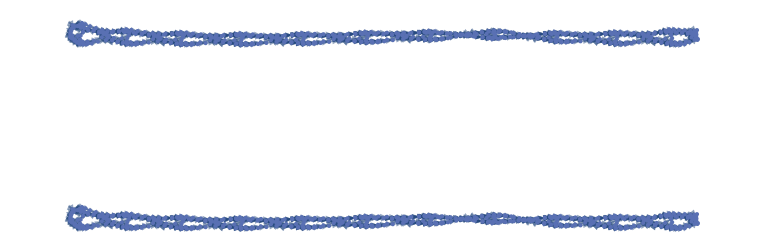

```mathematica
Graph[points, edges, GraphLayout->"SpringElectricalEmbedding"]
```

```mathematica
CanonicalFormCode20[list_]:=First[Sort[Last[FindTransientRepeat[StripZeros/@CellularAutomaton[{20, {2, 1}, 2}, {list, 0}, 100], 2]]]]
```